Symbolic integration of the cosine-weighted constant visibility function ∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
```

π

We can then assume that the Ambient Occlusion value of a flat, unoccluded surface should equal π, which is then scaled to 1 to be stored into a classical AO texture.
So let’s decide that an AO map’s value should be scaled by π when read by a shader, multiplied by ρ/πthe surface’s albedo to obtain a [0,1] ambient reflectance value, then multiplied by the irradiance perceived by the surface to finally obtain the reflected radiance in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π (π AO)E(x)=ρ AO E(x)

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0=1 and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.
We notice that E_0(x) is exactly the value computed for the Ambient Occlusion, so E_0(x)=AO.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).
We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=ρ/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ ρ/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that we can compute the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize = 100;
bouncesCount = 10;
rawArray= {
 BinaryReadList["WallHeight1.float", "Real32"],
BinaryReadList["WallHeight2.float", "Real32"],
BinaryReadList["WallHeight3.float", "Real32"],
BinaryReadList["WallHeight4.float", "Real32"]
};
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
```

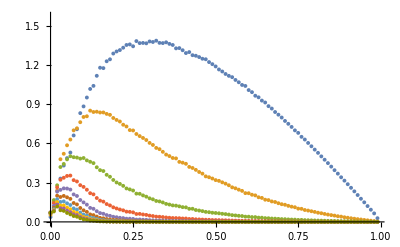

```mathematica
ListPlot[bounces,PlotRange->{0,π/2}]
```

Intuitively, it looks more and more like a normal distribution and we can model it as f(x)=a*x*(1-x)*e^-bx.
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[8*x*(1-x)*ⅇ^(-k*x),{x,0,1},PlotRange->{0,π/2}],{{k,1},0,20}]
```

{a→6.8839,b→1.55043}

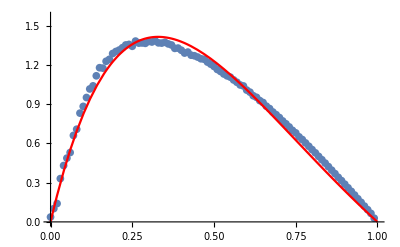

```mathematica
model=a*b*x*(1-x)*Exp[-b*x];
modelFit1=FindFit[bounces[[1]], model,{a,b},{x}]
bounce1=Function[{x},Evaluate[model/.modelFit1]];
Show[
ListPlot[bounces[[1]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce1[x],{x,0,1},PlotStyle->Red]
]
```

{a→2.77681,b→4.9367}

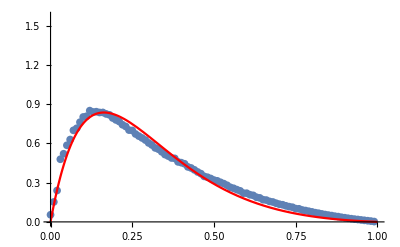

```mathematica
modelFit2=FindFit[bounces[[2]], model,{a,b},{x}]
bounce2=Function[{x},Evaluate[model/.modelFit2]];
Show[
ListPlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce2[x],{x,0,1},PlotStyle->Red]
]
```

{a→1.5086,b→9.62783}

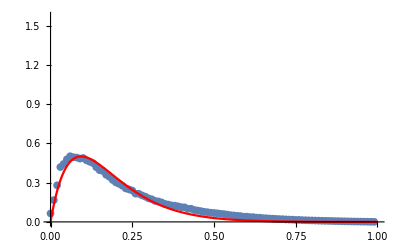

```mathematica
modelFit3=FindFit[bounces[[3]], model,{a,b},{x}]
bounce3=Function[{x},Evaluate[model/.modelFit3]];
Show[
ListPlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce3[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.994155,b→16.3854}

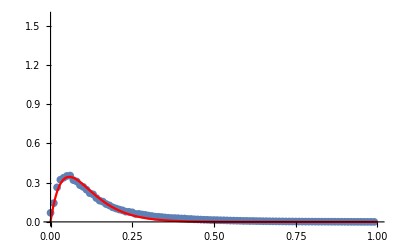

```mathematica
modelFit4=FindFit[bounces[[4]], model,{a,b},{x}]
bounce4=Function[{x},Evaluate[model/.modelFit4]];
Show[
ListPlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce4[x],{x,0,1},PlotStyle->Red]
]
```

{6.8839,2.77681,1.5086,0.994155}

{1.55043,4.9367,9.62783,16.3854}

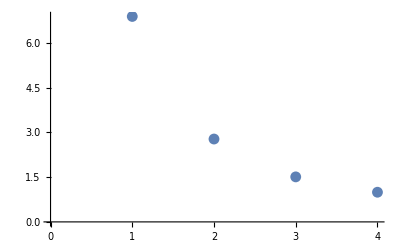

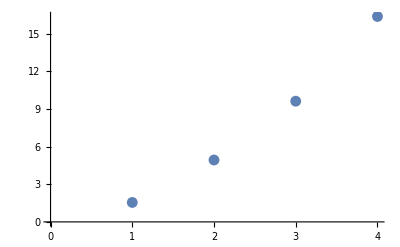

```mathematica
coeffsA={a/.modelFit1,a/.modelFit2,a/.modelFit3,a/.modelFit4}
coeffsB={b/.modelFit1,b/.modelFit2,b/.modelFit3,b/.modelFit4}
ListPlot[coeffsA]
ListPlot[coeffsB]
```